# Practical 1 Ujjwal Kumar Roll no.- 20211464 BSc(H) Computer Science Sem - IV

## Bisection Method

## Question 1 :

1th iteration value is:1.5

Estimated error in1th iteration is:0.5

2th iteration value is:1.75

Estimated error in2th iteration is:0.25

3th iteration value is:1.625

Estimated error in3th iteration is:0.125

4th iteration value is:1.5625

Estimated error in4th iteration is:0.0625

5th iteration value is:1.59375

Estimated error in5th iteration is:0.03125

6th iteration value is:1.57813

Estimated error in6th iteration is:0.015625

7th iteration value is:1.57031

Estimated error in7th iteration is:0.0078125

8th iteration value is:1.57422

Estimated error in8th iteration is:0.00390625

9th iteration value is:1.57227

Estimated error in9th iteration is:0.00195313

10th iteration value is:1.57129

Estimated error in10th iteration is:0.000976563

11th iteration value is:1.5708

Estimated error in11th iteration is:0.000488281

12th iteration value is:1.57056

Estimated error in12th iteration is:0.000244141

13th iteration value is:1.57068

Estimated error in13th iteration is:0.00012207

Return[1.57074]

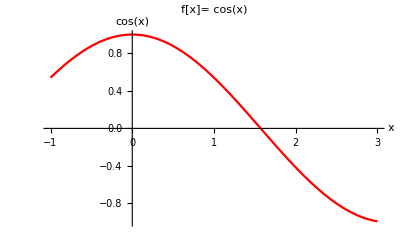

```mathematica
x0=1.0;
x1=2.0;
Nmax=20;
eps=0.0001;
f[x_]:=Cos[x];
If[N[f[x0]*f[x1]]>0,
Print["Your values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax, i++, m=(x0+x1)/2;
If[Abs[(x1-x0)/2]<eps, Return[m],
Print[i, "th iteration value is:", m];
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2];
If[f[m]*f[x1]>0, x1=m, x0=m]]];
Print["Root is:", m]*
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2]];
Plot[f[x], {x, -1, 3}, PlotRange->{-1, 1},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x, f[x]}]
```

## Question 2 :

1th iteration value is:0.5

Estimated error in1th iteration is:0.5

2th iteration value is:0.25

Estimated error in2th iteration is:0.25

3th iteration value is:0.125

Estimated error in3th iteration is:0.125

4th iteration value is:0.1875

Estimated error in4th iteration is:0.0625

5th iteration value is:0.21875

Estimated error in5th iteration is:0.03125

6th iteration value is:0.203125

Estimated error in6th iteration is:0.015625

7th iteration value is:0.195313

Estimated error in7th iteration is:0.0078125

8th iteration value is:0.199219

Estimated error in8th iteration is:0.00390625

9th iteration value is:0.201172

Estimated error in9th iteration is:0.00195313

10th iteration value is:0.202148

Estimated error in10th iteration is:0.000976563

11th iteration value is:0.20166

Estimated error in11th iteration is:0.000488281

12th iteration value is:0.201416

Estimated error in12th iteration is:0.000244141

13th iteration value is:0.201538

Estimated error in13th iteration is:0.00012207

Return[0.201599]

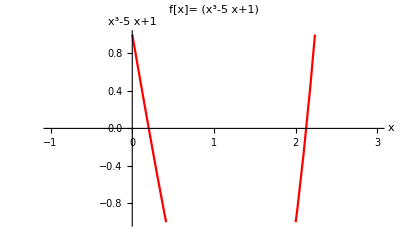

```mathematica
x0=0;
x1=1.0;
Nmax=20;
eps=0.0001;
f[x_]:=x^3-5x+1;
If[N[f[x0]*f[x1]]>0,
Print["Your values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax, i++, m=(x0+x1)/2;
If[Abs[(x1-x0)/2]<eps, Return[m],
Print[i, "th iteration value is:", m];
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2];
If[f[m]*f[x1]>0, x1=m, x0=m]]];
Print["Root is:", m]*
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2]];
Plot[f[x], {x, -1, 3}, PlotRange->{-1, 1},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x, f[x]}]
```

## Question 3 :

1th iteration value is:0.5

Estimated error in1th iteration is:0.5

2th iteration value is:0.75

Estimated error in2th iteration is:0.25

3th iteration value is:0.625

Estimated error in3th iteration is:0.125

4th iteration value is:0.5625

Estimated error in4th iteration is:0.0625

5th iteration value is:0.53125

Estimated error in5th iteration is:0.03125

6th iteration value is:0.515625

Estimated error in6th iteration is:0.015625

7th iteration value is:0.523438

Estimated error in7th iteration is:0.0078125

8th iteration value is:0.519531

Estimated error in8th iteration is:0.00390625

9th iteration value is:0.517578

Estimated error in9th iteration is:0.00195313

10th iteration value is:0.518555

Estimated error in10th iteration is:0.000976563

11th iteration value is:0.518066

Estimated error in11th iteration is:0.000488281

12th iteration value is:0.517822

Estimated error in12th iteration is:0.000244141

13th iteration value is:0.5177

Estimated error in13th iteration is:0.00012207

Return[0.517761]

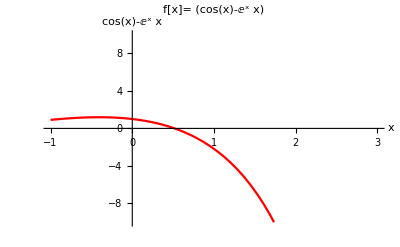

```mathematica
x0=0;
x1=1.0;
Nmax=20;
eps=0.0001;
f[x_]:=Cos[x]-x*Exp[x];
If[N[f[x0]*f[x1]]>0,
Print["Your values do not satisfy the IVP so change the value."],
For[i=1,i≤Nmax, i++, m=(x0+x1)/2;
If[Abs[(x1-x0)/2]<eps, Return[m],
Print[i, "th iteration value is:", m];
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2];
If[f[m]*f[x1]>0, x1=m, x0=m]]];
Print["Root is:", m]*
Print["Estimated error in", i, "th iteration is:", (x1-x0)/2]];
Plot[f[x], {x, -1, 3}, PlotRange->{-10, 10},
PlotStyle->Red, PlotLabel->"f[x]=" f[x], AxesLabel->{x, f[x]}]
```